```mathematica
(*Метод Эйлера*)
```

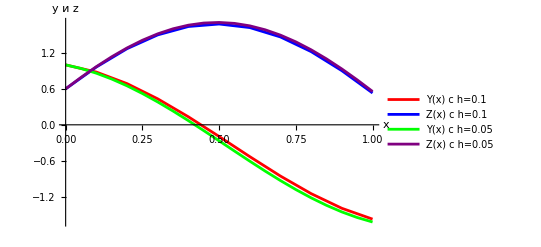

```mathematica
Clear[y, z]
a = 0;b = 1;y0 = 1;z0 = 0.6;h1 = 0.1;h2 = 0.05;   
n1 = Floor[(b - a)/h1]; n2 = Floor[(b - a)/h2];   
f[y_,z_]:=-2*z
g[y_,z_]:=3*y+1
eulerMethod[{y0_, z0_}, h_, n_] := 
  Module[{x = a, y = y0, z = z0, result = {{x, y, z}}},
    AppendTo[result, {x, y, z}];  
    For[i = 1, i <= n, i++,
      y = y + h * f[y, z]; 
      z = z + h * g[y, z]; 
      x = x + h;
      AppendTo[result, {x, y, z}];  
    ];
    result
  ];
eulerh1 = eulerMethod[{y0, z0}, h1, n1];
eulerh2 = eulerMethod[{y0, z0}, h2, n2];
ListLinePlot[
 {
  eulerh1[[All, {1, 2}]], eulerh1[[All, {1, 3}]], 
  eulerh2[[All, {1, 2}]], eulerh2[[All, {1, 3}]]
 },
 PlotStyle -> {Red, Blue, Green, Purple},
 PlotLegends -> {"Y(x) с h=0.1", "Z(x) с h=0.1",   "Y(x) с h=0.05", "Z(x) с h=0.05"},AxesLabel->{"x","y и z"},
 PlotRange -> All
]
```

```mathematica
(*Метод Рунге-Кутта*)
```

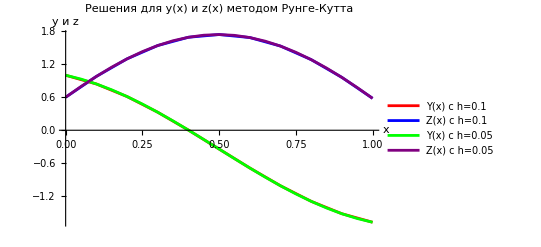

```mathematica
Clear[y,z]
a=0;b=1;y0=1;z0=0.6;h1=0.1;h2=0.05;      
n1=Floor[(b-a)/h1]; n2=Floor[(b-a)/h2];
f[y_,z_]:=-2*z
g[y_,z_]:=3*y+1
rungeKuttaMethod[{y0_,z0_},h_,n_]:=Module[{x=a,y=y0,z=z0,result={{x,y,z}}},AppendTo[result,{x,y,z}];
For[i=1,i<=n,i++,
{k1y,k1z}={h*f[y,z],h*g[y,z]};
{k2y,k2z}={h*f[y+0.5*k1y,z+0.5*k1z],h*g[y+0.5*k1y,z+0.5*k1z]};
{k3y,k3z}={h*f[y+0.5*k2y,z+0.5*k2z],h*g[y+0.5*k2y,z+0.5*k2z]};
{k4y,k4z}={h*f[y+k3y,z+k3z],h*g[y+k3y,z+k3z]};
y=y+(1/6) (k1y+2*k2y+2*k3y+k4y);
z=z+(1/6) (k1z+2*k2z+2*k3z+k4z);
x=x+h;
AppendTo[result,{x,y,z}];  ];
result];
rk1=rungeKuttaMethod[{y0,z0},h1,n1];
rk2=rungeKuttaMethod[{y0,z0},h2,n2];
ListLinePlot[{rk1[[All,{1,2}]],rk1[[All,{1,3}]],rk2[[All,{1,2}]],rk2[[All,{1,3}]]},PlotStyle->{Red,Blue,Green,Purple},PlotLegends->{"Y(x) с h=0.1","Z(x) с h=0.1","Y(x) с h=0.05","Z(x) с h=0.05"},AxesLabel->{"x","y и z"},PlotLabel->"Решения для y(x) и z(x) методом Рунге-Кутта",PlotRange->All]
```

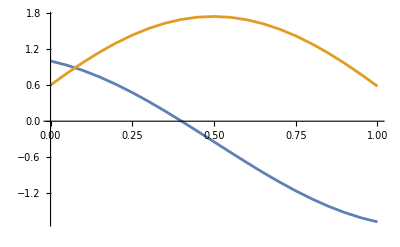

```mathematica
ListLinePlot[{rk2[[All,{1,2}]],rk2[[All,{1,3}]]},PlotRange->All]
```

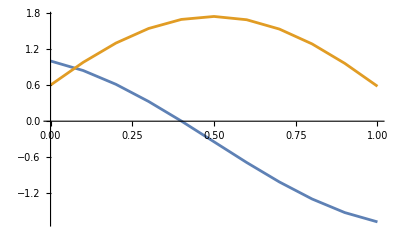

```mathematica
ListLinePlot[{rk1[[All,{1,2}]],rk1[[All,{1,3}]]},PlotRange->All]
```

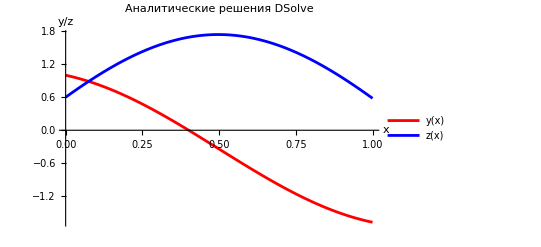

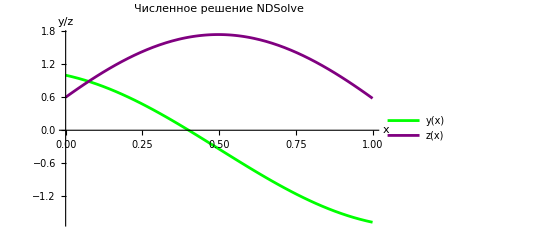

```mathematica
Clear[y,z]
eq1=y'[x]==-2z[x];
eq2=z'[x]==3*y[x]+1;
initialConditions={y[0]==1,z[0]==0.6};

solutionDSolve=DSolve[{eq1,eq2,initialConditions},{y,z},x];
ySolution=y[x]/. solutionDSolve[[1]];
zSolution=z[x]/. solutionDSolve[[1]];

Plot[{ySolution,zSolution},{x,0,1},PlotStyle->{Red,Blue},PlotLegends->{"y(x)","z(x)"},AxesLabel->{"x","y/z"},PlotLabel->"Аналитические решения DSolve"]

numericalSolution=NDSolve[{eq1,eq2,initialConditions},{y,z},{x,0,1}];

Plot[{y[x]/. numericalSolution,z[x]/. numericalSolution},{x,0,1},PlotStyle->{Green,Purple},PlotLegends->{"y(x)","z(x)"},AxesLabel->{"x","y/z"},PlotLabel->"Численное решение NDSolve"]
```